```mathematica
primitives=Select[Keys[Select[Select[$LifeData,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],IsPrimitive[Normal[$LifeData[#]["MatrixData"]]]&];
```

```mathematica
partcounts=ParallelMap[{#Name,#["Year"],If[#MatrixData["ExplicitLength"]<10^5,Length[CausalSeparation[#["MatrixData"]["ExplicitPositions"]]],TooBig]}&,$LifeData];
```

### Part counts histogram

```mathematica
partcounts = ;
```

```mathematica
(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])
```

<|1969→{1,1,1,1,1,1,1,1,1,1,1,1,1,1},1970→{1,1,1,1,1,1,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,1,1,4,1,1,1,1,1,1,1,1,1,1,10,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1},1971→{15,1,1,5,1,4,366,1,1,1,1,1,3,1,6,1,1,18,1,1,1,1,1,1,2,1,1,1,1,1,1,1,12,2,1,1,3,1,4,2,1,4,1,1,1,1,2,1,1,1,1,1,1,1,5,1,1,1,1,1,1,10},1972→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1},1973→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,40,7,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1976→{3,1,1,1,3},1977→{1,1,1,1,5,1,3,1,1},1978→{5,1,2},1979→{1},1980→{6,1,1,1,12},1982→{1,16,1},1983→{12,24,2,4},1984→{6,2,6,10,1,3,3,9,3},1985→{17,1},1986→{8},1988→{1,1,1},1989→{14,2,1,1,1,1,4,2,1,1,1,1,1,1,2,15,2,1,1,1,1,1,1,1,8,3},1990→{1,19,84,9,1,307,6},1991→{22,35,2,32,39,44,108,42,26,100,14},1992→{1,2,1,1,1,1,3,1,1,1,1,69,1,3,1,1,1,31,8,3,1,1,105,151,41,38,50,1,1,1,2,1},1993→{1,17,1,1,4,12,8,1,1,4,1,1,17,5,1,1,2,8},1994→{1,8,23,1,16,16,7,4,1,9,4,4,1,2,1,1,21,12,34,11,30,13,17,6,51,441,1,1,5,1,5,1,17,1,13,4,1,8},1995→{6,3,4,1,8,2,1,10,5,5,57,5,21,20,7,1,3,10,6},1996→{1,7,1,13,2,7,6,8,6,11,9,6,11,20,8,10,7,476,367,38,5,7,46,8,8,6,1,118,2,12},1997→{3,1,17,1,1,1,1,1,3,1,5,9,9,13,1,4,6,24,16,11,6,248,436,198,1,7,10,14,4,3,9,1,16,1,8},1998→{1,1,1,1,17,30,27,6,11,7,548,4,6,7,9,9,4,5,22,22,2,1,1,6,6},1999→{1,2,1,16,1},2000→{3,1,1,1,8,1,3,2,2,5,8,1,10,2,1,1},2001→{1,1,10,1,1,15,1,1},2002→{1,1,7,1,8,2,6,4,2,10,7},2003→{6,2500,1,1,1,12,32,2774},2004→{2,1,16,1,1,5,6,4,448,2,10,6,3},2005→{1,1,1,12,21,1,1,3,2,3,2,36,1,5,1,12,1},2006→{6,4,3,1,1,6,7,5,5548,5,1,4},2007→{7,12,4,16,12,2,7,13},2008→{1,3,2,TooBig,1,6},2009→{16,1,1,4,47,4,1,2,3,16,4,8,486,8,TooBig,19,6},2010→{15,1,4,1,12,3,24,1,20,114,1,1,5,47,1,2,8,7,7,8,5,19,34},2011→{216,5,1,1,12,6,2,1,1,1,9,5,1},2012→{2,1,6,16,14,12,2,5,6},2013→{3,1,2,10,9,8,1,2,24,24,6,155,3,5,1,4},2014→{4,5,1,3,3,12,3,1,1,18,5,217,16},2015→{1,1,9,7,1,4,8,3,3,4,3,43,7,20,10,6,8,6,40,383,18,19,21,24,4,5,8,4,7,6,2,10,6,10},2016→{5,5,16,4,14,238,28,1,1,1,2,1,10,11,6,11,8,10,9,5,9,10,9,529,1,2,2,10,4,1},2017→{1,1,10,12,9,8,5,8,10,13,12,13,5,1,5,4},2018→{3,1,5,1,1,1,16,2,14,3,1,11,2,56,9,9,15,9,3,20,4,11,10,327,1,2,7,9,8,5},2019→{1,1,1,2,3,7,7,9,8,3,1,10,3},2020→{2,9,5,1,20,1,8,2,5,8,24,5,1,TooBig,3,1},2021→{1,1,1,7,5,1,19,14,9,1,6,8,7,5,2,10,6,26,4,5,8,10,7,5,36,10,2,1,2,2,5,50,16,6,36,14,8,14,13,6,6,10,16,10,14,12,16,5,6,8,8},2022→{10,8,4,4,4,5,10,2,1,5,1,3,3,3,5,6,7,8,10,7,8,3,10,9,12,6,10,10,12,18,13,12,3,1,4,2,5,5,5,1,3,3,20,3,1,6,8,12,7,3,9,12,4,6,8,8,20,4,6,10,8,4,10,14,6,8,12,7,12,12,3,30,18,6,9,10,4,7,6,9,3,6,1,1,2,1,3,5,7,4,3,6,7,4,10,8,8,14,8,9,22,18,6,12,6,21,4,18,14,8,8,10,12,10,16,16,18,10,6,14,6,8,14,9,9,4,11,3,10,3,12,10,6,22,8,7,10,15,20,19,8,44,10,13,9,20,9,9,12,10,18,10,11,28,28,4,24,10,8,6,11,12,26,12,18,10,20,5,13,5,5,5,4,6,8,9,8,11,12,16,6,11,8,26,10,24,10,5,6,13,12,18,9,18,8,7,5,6},2023→{6,8,12,20,40,5,8,8,6,12,14,6,20,3,6,12,3,1,3,5,4,10,3,5,11,5,10,10,12,12,12,6,12,5,8,8,20,12,57,22,17,7,2,3,8,16,7,6,46,12,5,12,12,8,2,16,7,55,8,14,10,12,6,20,8,5,7,13,12,20,14,10,14,24,8,8,12,20,8,12,17,10,8,11,7,8,4,12,6,8,20,10,10,8,12,9,12,10,16,5,10,9,14,14,20,4,8,6,12,5,17,28,12,10,16,24,12,12,10,28,8,14,10,8,12,16,12,28,14,20,14,20,14,12,14,16,11,10,12,12,20,16,10,10,5,10,6,24,6,8,16,12,16,8,14,8,10,12,14,11,8,16,7,20,9,6,20,20,8,10,14,16,10,12,3,9,14,8,8,8,18,12,7,10,7,5,17,18,22,28,38,14,18,24},1975→{8},2024→{4,2,2,12,8,28,7,8,9,6,20,8,16,10,5},2025→{1}|>

```mathematica
# / Total[#]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])
```

<|1969→{1/14,1/14,1/14,1/14,1/14,1/14,1/14,1/14,1/14,1/14,1/14,1/14,1/14,1/14},1970→{1/79,1/79,1/79,1/79,1/79,1/79,1/79,4/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,4/79,1/79,1/79,1/79,4/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,10/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,3/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79,1/79},1971→{15/508,1/508,1/508,5/508,1/508,1/127,183/254,1/508,1/508,1/508,1/508,1/508,3/508,1/508,3/254,1/508,1/508,9/254,1/508,1/508,1/508,1/508,1/508,1/508,1/254,1/508,1/508,1/508,1/508,1/508,1/508,1/508,3/127,1/254,1/508,1/508,3/508,1/508,1/127,1/254,1/508,1/127,1/508,1/508,1/508,1/508,1/254,1/508,1/508,1/508,1/508,1/508,1/508,1/508,5/508,1/508,1/508,1/508,1/508,1/508,1/508,5/254},1972→{1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/16,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,3/64,3/64,1/32,1/64,1/64,1/64,1/64,1/32,1/64,1/64,1/64,1/64,1/64,1/32,1/64,1/64,1/64},1973→{1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,4/17,7/170,1/170,1/170,1/170,1/170,1/170,1/85,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170,1/170},1976→{1/3,1/9,1/9,1/9,1/3},1977→{1/15,1/15,1/15,1/15,1/3,1/15,1/5,1/15,1/15},1978→{5/8,1/8,1/4},1979→{1},1980→{2/7,1/21,1/21,1/21,4/7},1982→{1/18,8/9,1/18},1983→{2/7,4/7,1/21,2/21},1984→{6/43,2/43,6/43,10/43,1/43,3/43,3/43,9/43,3/43},1985→{17/18,1/18},1986→{1},1988→{1/3,1/3,1/3},1989→{14/69,2/69,1/69,1/69,1/69,1/69,4/69,2/69,1/69,1/69,1/69,1/69,1/69,1/69,2/69,5/23,2/69,1/69,1/69,1/69,1/69,1/69,1/69,1/69,8/69,1/23},1990→{1/427,19/427,12/61,9/427,1/427,307/427,6/427},1991→{11/232,35/464,1/232,2/29,39/464,11/116,27/116,21/232,13/232,25/116,7/232},1992→{1/525,2/525,1/525,1/525,1/525,1/525,1/175,1/525,1/525,1/525,1/525,23/175,1/525,1/175,1/525,1/525,1/525,31/525,8/525,1/175,1/525,1/525,1/5,151/525,41/525,38/525,2/21,1/525,1/525,1/525,2/525,1/525},1993→{1/86,17/86,1/86,1/86,2/43,6/43,4/43,1/86,1/86,2/43,1/86,1/86,17/86,5/86,1/86,1/86,1/43,4/43},1994→{1/793,8/793,23/793,1/793,16/793,16/793,7/793,4/793,1/793,9/793,4/793,4/793,1/793,2/793,1/793,1/793,21/793,12/793,34/793,11/793,30/793,1/61,17/793,6/793,51/793,441/793,1/793,1/793,5/793,1/793,5/793,1/793,17/793,1/793,1/61,4/793,1/793,8/793},1995→{6/175,3/175,4/175,1/175,8/175,2/175,1/175,2/35,1/35,1/35,57/175,1/35,3/25,4/35,1/25,1/175,3/175,2/35,6/175},1996→{1/1227,7/1227,1/1227,13/1227,2/1227,7/1227,2/409,8/1227,2/409,11/1227,3/409,2/409,11/1227,20/1227,8/1227,10/1227,7/1227,476/1227,367/1227,38/1227,5/1227,7/1227,46/1227,8/1227,8/1227,2/409,1/1227,118/1227,2/1227,4/409},1997→{3/1090,1/1090,17/1090,1/1090,1/1090,1/1090,1/1090,1/1090,3/1090,1/1090,1/218,9/1090,9/1090,13/1090,1/1090,2/545,3/545,12/545,8/545,11/1090,3/545,124/545,2/5,99/545,1/1090,7/1090,1/109,7/545,2/545,3/1090,9/1090,1/1090,8/545,1/1090,4/545},1998→{1/754,1/754,1/754,1/754,17/754,15/377,27/754,3/377,11/754,7/754,274/377,2/377,3/377,7/754,9/754,9/754,2/377,5/754,11/377,11/377,1/377,1/754,1/754,3/377,3/377},1999→{1/21,2/21,1/21,16/21,1/21},2000→{3/50,1/50,1/50,1/50,4/25,1/50,3/50,1/25,1/25,1/10,4/25,1/50,1/5,1/25,1/50,1/50},2001→{1/31,1/31,10/31,1/31,1/31,15/31,1/31,1/31},2002→{1/49,1/49,1/7,1/49,8/49,2/49,6/49,4/49,2/49,10/49,1/7},2003→{6/5327,2500/5327,1/5327,1/5327,1/5327,12/5327,32/5327,2774/5327},2004→{2/505,1/505,16/505,1/505,1/505,1/101,6/505,4/505,448/505,2/505,2/101,6/505,3/505},2005→{1/104,1/104,1/104,3/26,21/104,1/104,1/104,3/104,1/52,3/104,1/52,9/26,1/104,5/104,1/104,3/26,1/104},2006→{6/5591,4/5591,3/5591,1/5591,1/5591,6/5591,7/5591,5/5591,5548/5591,5/5591,1/5591,4/5591},2007→{7/73,12/73,4/73,16/73,12/73,2/73,7/73,13/73},2008→{1/(13+TooBig),3/(13+TooBig),2/(13+TooBig),TooBig/(13+TooBig),1/(13+TooBig),6/(13+TooBig)},2009→{16/(626+TooBig),1/(626+TooBig),1/(626+TooBig),4/(626+TooBig),47/(626+TooBig),4/(626+TooBig),1/(626+TooBig),2/(626+TooBig),3/(626+TooBig),16/(626+TooBig),4/(626+TooBig),8/(626+TooBig),486/(626+TooBig),8/(626+TooBig),TooBig/(626+TooBig),19/(626+TooBig),6/(626+TooBig)},2010→{3/68,1/340,1/85,1/340,3/85,3/340,6/85,1/340,1/17,57/170,1/340,1/340,1/68,47/340,1/340,1/170,2/85,7/340,7/340,2/85,1/68,19/340,1/10},2011→{24/29,5/261,1/261,1/261,4/87,2/87,2/261,1/261,1/261,1/261,1/29,5/261,1/261},2012→{1/32,1/64,3/32,1/4,7/32,3/16,1/32,5/64,3/32},2013→{1/86,1/258,1/129,5/129,3/86,4/129,1/258,1/129,4/43,4/43,1/43,155/258,1/86,5/258,1/258,2/129},2014→{4/289,5/289,1/289,3/289,3/289,12/289,3/289,1/289,1/289,18/289,5/289,217/289,16/289},2015→{1/711,1/711,1/79,7/711,1/711,4/711,8/711,1/237,1/237,4/711,1/237,43/711,7/711,20/711,10/711,2/237,8/711,2/237,40/711,383/711,2/79,19/711,7/237,8/237,4/711,5/711,8/711,4/711,7/711,2/237,2/711,10/711,2/237,10/711},2016→{5/963,5/963,16/963,4/963,14/963,238/963,28/963,1/963,1/963,1/963,2/963,1/963,10/963,11/963,2/321,11/963,8/963,10/963,1/107,5/963,1/107,10/963,1/107,529/963,1/963,2/963,2/963,10/963,4/963,1/963},2017→{1/117,1/117,10/117,4/39,1/13,8/117,5/117,8/117,10/117,1/9,4/39,1/9,5/117,1/117,5/117,4/117},2018→{3/566,1/566,5/566,1/566,1/566,1/566,8/283,1/283,7/283,3/566,1/566,11/566,1/283,28/283,9/566,9/566,15/566,9/566,3/566,10/283,2/283,11/566,5/283,327/566,1/566,1/283,7/566,9/566,4/283,5/566},2019→{1/56,1/56,1/56,1/28,3/56,1/8,1/8,9/56,1/7,3/56,1/56,5/28,3/56},2020→{2/(95+TooBig),9/(95+TooBig),5/(95+TooBig),1/(95+TooBig),20/(95+TooBig),1/(95+TooBig),8/(95+TooBig),2/(95+TooBig),5/(95+TooBig),8/(95+TooBig),24/(95+TooBig),5/(95+TooBig),1/(95+TooBig),TooBig/(95+TooBig),3/(95+TooBig),1/(95+TooBig)},2021→{1/500,1/500,1/500,7/500,1/100,1/500,19/500,7/250,9/500,1/500,3/250,2/125,7/500,1/100,1/250,1/50,3/250,13/250,1/125,1/100,2/125,1/50,7/500,1/100,9/125,1/50,1/250,1/500,1/250,1/250,1/100,1/10,4/125,3/250,9/125,7/250,2/125,7/250,13/500,3/250,3/250,1/50,4/125,1/50,7/250,3/125,4/125,1/100,3/250,2/125,2/125},2022→{10/1877,8/1877,4/1877,4/1877,4/1877,5/1877,10/1877,2/1877,1/1877,5/1877,1/1877,3/1877,3/1877,3/1877,5/1877,6/1877,7/1877,8/1877,10/1877,7/1877,8/1877,3/1877,10/1877,9/1877,12/1877,6/1877,10/1877,10/1877,12/1877,18/1877,13/1877,12/1877,3/1877,1/1877,4/1877,2/1877,5/1877,5/1877,5/1877,1/1877,3/1877,3/1877,20/1877,3/1877,1/1877,6/1877,8/1877,12/1877,7/1877,3/1877,9/1877,12/1877,4/1877,6/1877,8/1877,8/1877,20/1877,4/1877,6/1877,10/1877,8/1877,4/1877,10/1877,14/1877,6/1877,8/1877,12/1877,7/1877,12/1877,12/1877,3/1877,30/1877,18/1877,6/1877,9/1877,10/1877,4/1877,7/1877,6/1877,9/1877,3/1877,6/1877,1/1877,1/1877,2/1877,1/1877,3/1877,5/1877,7/1877,4/1877,3/1877,6/1877,7/1877,4/1877,10/1877,8/1877,8/1877,14/1877,8/1877,9/1877,22/1877,18/1877,6/1877,12/1877,6/1877,21/1877,4/1877,18/1877,14/1877,8/1877,8/1877,10/1877,12/1877,10/1877,16/1877,16/1877,18/1877,10/1877,6/1877,14/1877,6/1877,8/1877,14/1877,9/1877,9/1877,4/1877,11/1877,3/1877,10/1877,3/1877,12/1877,10/1877,6/1877,22/1877,8/1877,7/1877,10/1877,15/1877,20/1877,19/1877,8/1877,44/1877,10/1877,13/1877,9/1877,20/1877,9/1877,9/1877,12/1877,10/1877,18/1877,10/1877,11/1877,28/1877,28/1877,4/1877,24/1877,10/1877,8/1877,6/1877,11/1877,12/1877,26/1877,12/1877,18/1877,10/1877,20/1877,5/1877,13/1877,5/1877,5/1877,5/1877,4/1877,6/1877,8/1877,9/1877,8/1877,11/1877,12/1877,16/1877,6/1877,11/1877,8/1877,26/1877,10/1877,24/1877,10/1877,5/1877,6/1877,13/1877,12/1877,18/1877,9/1877,18/1877,8/1877,7/1877,5/1877,6/1877},2023→{6/2399,8/2399,12/2399,20/2399,40/2399,5/2399,8/2399,8/2399,6/2399,12/2399,14/2399,6/2399,20/2399,3/2399,6/2399,12/2399,3/2399,1/2399,3/2399,5/2399,4/2399,10/2399,3/2399,5/2399,11/2399,5/2399,10/2399,10/2399,12/2399,12/2399,12/2399,6/2399,12/2399,5/2399,8/2399,8/2399,20/2399,12/2399,57/2399,22/2399,17/2399,7/2399,2/2399,3/2399,8/2399,16/2399,7/2399,6/2399,46/2399,12/2399,5/2399,12/2399,12/2399,8/2399,2/2399,16/2399,7/2399,55/2399,8/2399,14/2399,10/2399,12/2399,6/2399,20/2399,8/2399,5/2399,7/2399,13/2399,12/2399,20/2399,14/2399,10/2399,14/2399,24/2399,8/2399,8/2399,12/2399,20/2399,8/2399,12/2399,17/2399,10/2399,8/2399,11/2399,7/2399,8/2399,4/2399,12/2399,6/2399,8/2399,20/2399,10/2399,10/2399,8/2399,12/2399,9/2399,12/2399,10/2399,16/2399,5/2399,10/2399,9/2399,14/2399,14/2399,20/2399,4/2399,8/2399,6/2399,12/2399,5/2399,17/2399,28/2399,12/2399,10/2399,16/2399,24/2399,12/2399,12/2399,10/2399,28/2399,8/2399,14/2399,10/2399,8/2399,12/2399,16/2399,12/2399,28/2399,14/2399,20/2399,14/2399,20/2399,14/2399,12/2399,14/2399,16/2399,11/2399,10/2399,12/2399,12/2399,20/2399,16/2399,10/2399,10/2399,5/2399,10/2399,6/2399,24/2399,6/2399,8/2399,16/2399,12/2399,16/2399,8/2399,14/2399,8/2399,10/2399,12/2399,14/2399,11/2399,8/2399,16/2399,7/2399,20/2399,9/2399,6/2399,20/2399,20/2399,8/2399,10/2399,14/2399,16/2399,10/2399,12/2399,3/2399,9/2399,14/2399,8/2399,8/2399,8/2399,18/2399,12/2399,7/2399,10/2399,7/2399,5/2399,17/2399,18/2399,22/2399,28/2399,38/2399,14/2399,18/2399,24/2399},1975→{1},2024→{4/145,2/145,2/145,12/145,8/145,28/145,7/145,8/145,9/145,6/145,4/29,8/145,16/145,2/29,1/29},2025→{1}|>

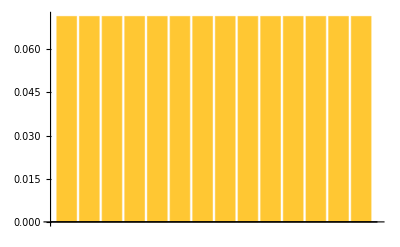
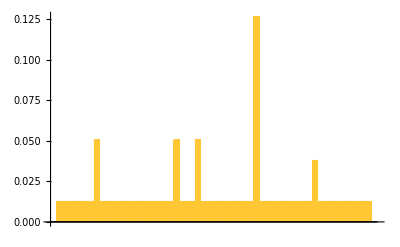
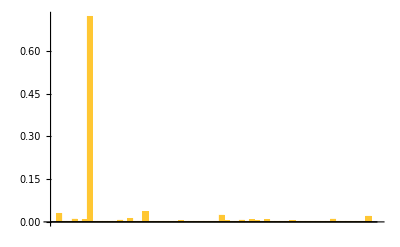
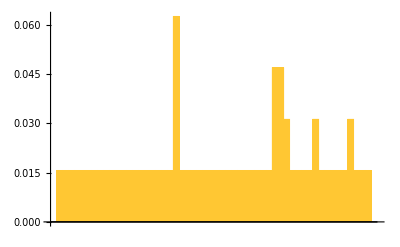
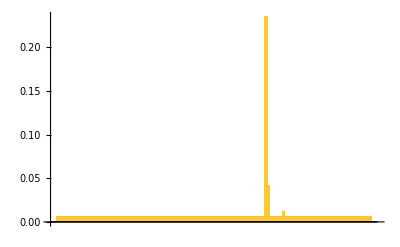
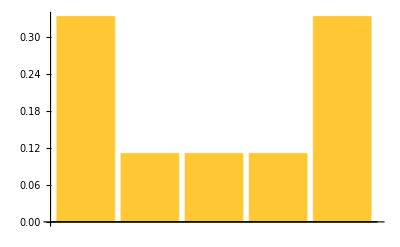
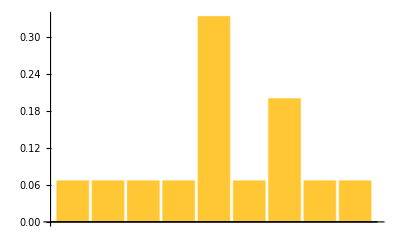
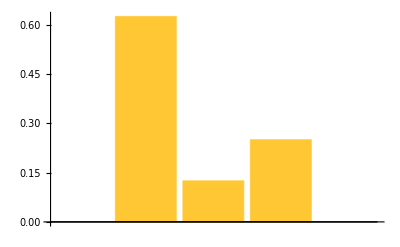
<|1969→-Graphics-,1970→-Graphics-,1971→-Graphics-,1972→-Graphics-,1973→-Graphics-,1976→-Graphics-,1977→-Graphics-,1978→-Graphics-,1979→-Graphics-,1980→-Graphics-,1982→-Graphics-,1983→-Graphics-,1984→-Graphics-,1985→-Graphics-,1986→-Graphics-,1988→-Graphics-,1989→-Graphics-,1990→-Graphics-,1991→-Graphics-,1992→-Graphics-,1993→-Graphics-,1994→-Graphics-,1995→-Graphics-,1996→-Graphics-,1997→-Graphics-,1998→-Graphics-,1999→-Graphics-,2000→-Graphics-,2001→-Graphics-,2002→-Graphics-,2003→-Graphics-,2004→-Graphics-,2005→-Graphics-,2006→-Graphics-,2007→-Graphics-,2008→-Graphics-,2009→-Graphics-,2010→-Graphics-,2011→-Graphics-,2012→-Graphics-,2013→-Graphics-,2014→-Graphics-,2015→-Graphics-,2016→-Graphics-,2017→-Graphics-,2018→-Graphics-,2019→-Graphics-,2020→-Graphics-,2021→-Graphics-,2022→-Graphics-,2023→-Graphics-,1975→-Graphics-,2024→-Graphics-,2025→-Graphics-|>

```mathematica
BarChart[# / Total[#]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])
```

```mathematica
With[{mcs = Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])},
ListPointPlot3D[Transpose[Values[mcs]], PlotRange->All, Filling->Axis,FillingStyle->Thick]
]
```

-Graphics3D-

```mathematica
With[{mcs = Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])},
ListPointPlot3D[Transpose[Values[mcs]], PlotRange->All, Filling->Axis,FillingStyle->Thick, ScalingFunctions->"Log"]
]
```

-Graphics3D-

```mathematica
With[{mcs = Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])},
ListPointPlot3D[Values[mcs], PlotRange->All, Filling->Axis,FillingStyle->Thick, ScalingFunctions->"Log"]
]
```

-Graphics3D-

```mathematica
d = Transpose[Values[Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])
]];
```

```mathematica
Length[d[[1]]]
```

54

```mathematica
DiscretePlot3D[d[[j, i]], {i, 1, Length[d[[1]]]}, {j, 1, Length[d]}, ExtentSize->Full, ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
DiscretePlot3D[d[[i, j]], {i, 1, Length[d]}, {j, 1, Length[d[[1]]]}, ExtentSize->Full, ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
With[{mcs = Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])},
ListPlot3D[Transpose[Values[mcs]], PlotRange->All, Filling->Axis,FillingStyle->Thick, ScalingFunctions->"Log"]
]
```

-Graphics3D-

```mathematica
With[{mcs = Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])},
ListLinePlot3D[Transpose[Values[mcs]], PlotRange->All, Filling->Axis, ScalingFunctions->"Log"]
]
```

-Graphics3D-

```mathematica
With[{mcs = Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])},
ListLinePlot3D[Transpose[Values[mcs]], PlotRange->All, Filling->Axis]
]
```

-Graphics3D-

```mathematica
With[{mcs = Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])},
ListLinePlot3D[Reverse/@Values[mcs], PlotRange->All, Filling->Axis]
]
```

-Graphics3D-

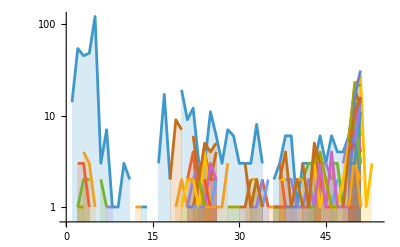

```mathematica
With[{mcs = Append[Table[Count[#,i],{i,20}],Length[Select[#,#>20&]]]&/@(Values/@Map[Last,GroupBy[partcounts,#[[2]]&],{2}])},
ListLinePlot[Transpose[Values[mcs]], PlotRange->All, Filling->Axis, ScalingFunctions->"Log"]
]
```

### Other

```mathematica
g = GroupBy[Values@$LifeData, #Year&];
```

#### arrayplots

```mathematica
KeySort[Map[If[#MatrixData["ExplicitLength"]<10^5, ArrayPlot[#MatrixData, ImageSize->{40, 40}], TooBig]&, g, {2}]]
```

<|1969→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1970→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1971→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1972→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1973→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1975→{-Graphics-},1976→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1977→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1978→{-Graphics-,-Graphics-,-Graphics-},1979→{-Graphics-},1980→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1982→{-Graphics-,-Graphics-,-Graphics-},1983→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},1984→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1985→{-Graphics-,-Graphics-},1986→{-Graphics-},1988→{-Graphics-,-Graphics-,-Graphics-},1989→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1990→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1991→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1992→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1993→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1994→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1995→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1996→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1997→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1998→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1999→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2000→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2001→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2002→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2003→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2004→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2005→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2006→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2007→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2008→{-Graphics-,-Graphics-,-Graphics-,TooBig,-Graphics-,-Graphics-},2009→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,TooBig,-Graphics-,-Graphics-},2010→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2011→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2012→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2013→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2014→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2015→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2016→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2017→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2018→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2019→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2020→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,TooBig,-Graphics-,-Graphics-},2021→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2022→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2023→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2024→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2025→{-Graphics-}|>

#### connected graphs

```mathematica
KeySort[Map[If[#MatrixData["ExplicitLength"]<10^5, NearestNeighborGraph[#MatrixData["ExplicitPositions"],
{All,2Sqrt[2]}, ImageSize->{40, 40}], TooBig]&,g, {2}]]
```

<|1969→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1970→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1971→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1972→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1973→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1975→{-Graphics-},1976→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1977→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1978→{-Graphics-,-Graphics-,-Graphics-},1979→{-Graphics-},1980→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1982→{-Graphics-,-Graphics-,-Graphics-},1983→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},1984→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1985→{-Graphics-,-Graphics-},1986→{-Graphics-},1988→{-Graphics-,-Graphics-,-Graphics-},1989→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1990→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1991→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1992→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1993→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1994→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1995→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1996→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1997→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1998→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1999→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2000→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2001→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2002→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2003→{-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,},2004→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2005→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2006→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-},2007→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2008→{-Graphics-,-Graphics-,-Graphics-,TooBig,-Graphics-,-Graphics-},2009→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,TooBig,-Graphics-,-Graphics-},2010→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2011→{,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2012→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2013→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2014→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-},2015→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2016→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2017→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2018→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2019→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2020→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,TooBig,-Graphics-,-Graphics-},2021→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2022→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2023→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2024→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2025→{-Graphics-}|>

#### When were primitives discovered?

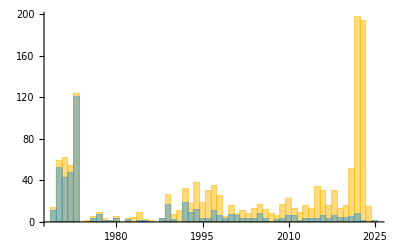

```mathematica
Histogram[{#Year&/@ $LifeData, $LifeData[#, "Year"]&/@primitives}, {1}]
```

### All patterns with primitives highlighted